## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Join[$Path,{NotebookDirectory[]}];
```

```mathematica
<<utilities.wl
```

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[α, o,max,CH]];
Symbolize[Subscript[α, o,max,EMIC]];
Symbolize[Subscript[α, o,max]];
Symbolize[Subscript[α, LC]];
Symbolize[Subscript[D, αα,CH]];
Symbolize[Subscript[D, αα,EMIC]];
```

All quantities are in Gaussian cgs units

Ω_ce0 electron equatorial gyro-frequency;
Ω_cp0 proton equatorial gyro-frequency;
Ω_pe0 plasma frequency
erg in MeV unit

Statistics of intense hydrogen band EMIC waves show normalized mean frequencies ω_EMIC/Ω_cp0 ∼ 0.3–0.7

```mathematica
c=Quantity[, "SpeedOfLight"];me0=Entity["Particle","Electron"][EntityProperty["Particle","Mass"]];
γ[erg_,m_]:=erg/(m c^2)+1;
```

```mathematica
addColumnToDataset[dataset_Dataset,column:_List,columnName:_String]/;Length[column]===Length[dataset]:=addColumnToDataset[dataset,{column},{columnName}];

addColumnToDataset[dataset_Dataset,columns:{__List},columnNames:{__String}]/;And[Length[columnNames]===Length[columns],Length[dataset]===Dimensions[columns][[2]]]:=Dataset@Transpose@Join[Transpose[dataset],Dataset[AssociationThread[columnNames,columns]]];
```

## Using plasmasphere density model

For the plasmasphere the average number density (in cm^-3) as a function of L shell (3 <=L<=7) was found to be  n_p = 1390 (3/L)^4.8 ± 440 (3/L)^3.6. For the trough the average number density (in cm^-3) as a function of  -shell (3 <=L<=7) and magnetic local time (0 • LT • 24) was found to be n_t = 124 (3/L)^4.0 + 36 (3/L)^3.5 Cos [(LT - (7.7 (3/L)^2.0 + 12) )π/12)  ±(78 (3/L)^4.72 + 17 (3/L)^3.75 Cos[(LT- 22) π/12]) .

```mathematica
np[l_]:=(1390 (3/l)^4.8±440 (3/l)^3.6)Quantity[, "Centimeters"]^-3
nt[l_,mlt_:0]:=124 (3/l)^4.0+36 (3/l)^3.5 Cos[(mlt-(7.7 (3/l)^2.0+12)) π/12]±(78 (3/l)^4.72+17 (3/l)^3.75 Cos[(mlt-22) π/12])

np[l_]:=(1390 (3/l)^4.8)Quantity[, "Centimeters"]^-3
nt[l_,mlt_:0]:=(124 (3/l)^4.0+36 (3/l)^3.5 Cos[(mlt-(7.7 (3/l)^2.0+12)) π/12]) Quantity[, "Centimeters"]^-3
```

Using formulary from NRL (All quantities are in Gaussian cgs)... μ= m_i/m_p; Z is charge state;

```mathematica
Subscript[Ω, pe0][n_]:=5.64 10^4(n/Quantity[, "Centimeters"]^-3)^(1/2)Quantity[, "Seconds"]^-1
Subscript[Ω, ce0][mag_]:=1.76 10^7 mag/Quantity[, "Gauss"] Quantity[, "Seconds"]^-1
Subscript[Ω, ci0][mag_,z_,μ_]:=9.58 10^3 z μ^-1 mag/Quantity[, "Gauss"] Quantity[, "Seconds"]^-1
Subscript[Ω, cp0][mag_]:=Subscript[Ω, ci0][mag,1,1]
```

The dipole magnetic moment of the Earth is tilted about 10.2 ° to the rotation axis, with a present -day moment of about 7.8 10^15 T m^3   or 30.2 μT  R_E^3.

```mathematica
dipoleM=UnitConvert[Quantity[30.2,"Microteslas"],"Gauss"]
```

0.302 G

```mathematica
dipoleMag[l_]:=dipoleM/l^3
```

```mathematica
Echo [np [3]];
Echo [np [7]];
Echo [nt [3,20]];
Echo[nt [3,8]];
```

1390. /cm^3

23.8082 /cm^3

159.889 /cm^3

88.111 /cm^3

In order for gyro-resonance to take place, electrons must possess a minimum kinetic energy E_min which depends on the value of the ratio (electron plasma frequency/electron gyro-frequency)

```mathematica
(*αTemp=Subscript[Ω, pe0]/Subscript[Ω, ce0]/.{Subscript[Ω, pe0]->Subscript[Ω, pe0][np[L]],Subscript[Ω, ce0]->Subscript[Ω, ce0][dipoleMag[L]]}*)
αTemp=Subscript[Ω,pe0]/Subscript[Ω,ce0]/. {Subscript[Ω, pe0]->Subscript[Ω, pe0][np[L]],Subscript[Ω, ce0]->Subscript[Ω, ce0][dipoleMag[L]]};
tempPlot:=Plot[αTemp,{L,1,8}]
```

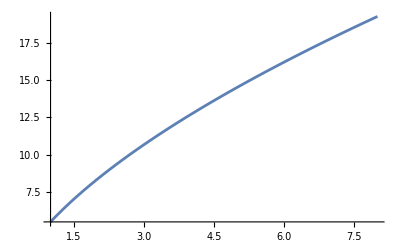

```mathematica
tempPlot
```

```mathematica
Subscript[α, LC,eq]:=(4 L^6-3 L^5)^(-1/4);
```

## EMIC wave

maximum resonant pitch angle α_(o,max),
Question: can we obtain it from observation? No, impossible from ELFIN

```mathematica
dispersionRelation=Cos[Subscript[α,o,max,CH]]==RHS;
```

```mathematica
(*RHS =Subscript[Ω, ce0]^2/(2 Subscript[ω, EMIC] Subscript[Ω, pe0])√(((1-Subscript[ω, EMIC]/Subscript[Ω, cp0])(Subscript[m, e]/Subscript[m, p]))/((1-Subscript[Ω, cp0](1-Subscript[η, p])/Subscript[ω, EMIC])(erg^2+erg)));*)
RHS =Subscript[Ω, ce0]^2/(2 Subscript[ω, EMIC] Subscript[Ω, pe0])√(((1-Subscript[ω, EMIC]/Subscript[Ω, cp0])(Subscript[m, e]/Subscript[m, p]))/(erg^2+erg));
Subscript[α, o,max,EMIC,raw]=ArcCos[RHS ]/Degree;
Subscript[α, o,max,EMIC]=Subscript[α, o,max,EMIC,raw]/.{Subscript[m, p]->Entity["Particle","Proton"][EntityProperty["Particle","Mass"]],Subscript[m, e]->Entity["Particle","Electron"][EntityProperty["Particle","Mass"]],Subscript[η, p]->0.8, Subscript[ω, EMIC]->c1 Subscript[Ω, cp0]}/.{Subscript[Ω, pe0]->20 Subscript[Ω, ce0],Subscript[Ω, cp0]->Subscript[Ω, ce0]/1837};
```

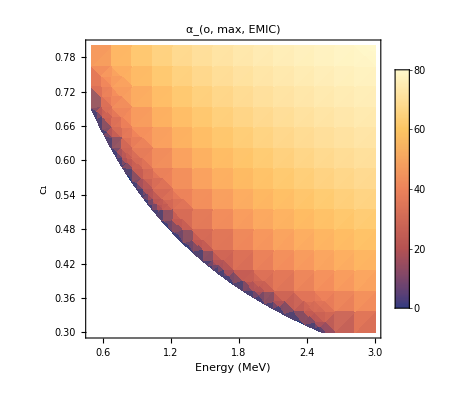

```mathematica
DensityPlot[ Subscript[α, o,max,EMIC],{erg,0.5,3},{c1,0.3,0.8},
PlotLegends->Automatic,PlotRange->All,
PlotLabel->"α_(o, max, EMIC)",FrameLabel->{{"c_1",""},{"Energy (MeV)",""}},
PlotLayout->"Row"]
```

```mathematica
Subscript[α, o,max,EMIC]=Subscript[α, o,max,EMIC,raw]/.{Subscript[m, p]->Entity["Particle","Proton"][EntityProperty["Particle","Mass"]],Subscript[m, e]->Entity["Particle","Electron"][EntityProperty["Particle","Mass"]],Subscript[η, p]->0.8, Subscript[ω, EMIC]->c1 Subscript[Ω, cp0]}/.{Subscript[Ω, ce0]->Subscript[Ω, ce0][dipoleMag[L]],Subscript[Ω, cp0]->Subscript[Ω, cp0][dipoleMag[L]],Subscript[Ω, pe0]->Subscript[Ω, pe0][np[L]]};
```

```mathematica
DensityPlot[ {Subscript[α, o,max,EMIC]/.{L->5},Subscript[α, o,max,EMIC]/.{L->6}},{erg,0.5,3},{c1,0.3,0.8},
PlotLegends->Automatic,PlotRange->All,
PlotLabel->"α_(o, max, EMIC)",FrameLabel->{{"c_1",""},{"Energy (MeV)","L=5\tL=6"}},
PlotLayout->"Row"]
(*Plot3D[ Subscript[α, o,max,EMIC]/.{L->5},{erg,0.5,3},{c1,0.3,0.8},AxesLabel->Automatic]*)
(*Plot3D[ Subscript[α, o,max,EMIC]/.{L->6},{erg,0.5,3},{c1,0.3,0.8},AxesLabel->Automatic]*)
```

-Graphics-

#### Export data

```mathematica
c1List=Subdivide[0.3,0.8,100];
ergList=Subdivide[0.5,3,100];
lList={5,6};
dataset=Dataset[AssociationThread[{"energy","c1","L_bins"},#]&/@Tuples[{ergList,c1List,lList}]];
updatedDataset = addColumnToDataset[dataset,Flatten@Table[Subscript[α, o,max,EMIC],{erg,ergList},{c1,c1List},{L,lList}],"alpha"]
Export["../data/alpha_max_EMIC.csv",updatedDataset[Select[FreeQ[_Complex]],{"alpha"->QuantityMagnitude}]];
```

Dataset[<>]

## Chorus wave

The corresponding maximum pitch angle for cyclotron resonance (0.5 Ω_ce0)/((E^2+E) (ω_(m,CH)+Δ𝜔_CH))(Ω_ce0/Ω_pe0 )_CH

```mathematica
RHS=(0.5 Subscript[Ω, ce0])/((erg^2+erg) (Subscript[ω, m,CH]+Subscript[Δω, CH]))(Subscript[Ω, ce0]/Subscript[Ω, pe0] );
Subscript[α, o,max,CH]=ArcCos[RHS ]/Degree;
Subscript[α, o,max,CH]=Subscript[α, o,max,CH]/.{Subscript[ω, m,CH]->c2 Subscript[Ω, ce0],Subscript[Δω, CH]->0}/.{Subscript[Ω, ce0]->Subscript[Ω, ce0][dipoleMag[L]],Subscript[Ω, cp0]->Subscript[Ω, cp0][dipoleMag[L]],Subscript[Ω, pe0]->Subscript[Ω, pe0][nt[L,mlt]]};
```

```mathematica
(*DensityPlot[ {Subscript[α, o,max,CH]/.{L->5,mlt->0},Subscript[α, o,max,CH]/.{L->6,mlt->0}},{erg,0.5,3},{c2,0.1,0.5},
Mesh->Automatic,MeshFunctions->{#3&,#3&},PlotLegends->Automatic,PlotRange->All,
PlotLabel->"α_(o, max, CH)",FrameLabel->{{"c_2",""},{"Energy (MeV)","L=5\tL=6"}},
PlotLayout->"Row"]//Rasterize
Export["../figures/aCH_c2.pdf",%];

DensityPlot[ {Subscript[α, o,max,CH]/.{L->5,c2->0.3},Subscript[α, o,max,CH]/.{L->6,c2->0.3}},{erg,0.5,3},{mlt,0,24},
Mesh->Automatic,MeshFunctions->{#3&,#3&},PlotLegends->Automatic,PlotRange->All,
PlotLabel->"α_(o, max, CH)",FrameLabel->{{"MLT",""},{"Energy (MeV)","L=5\tL=6"}},
PlotLayout->"Row"]//Rasterize
Export["../figures/aCH_MLT.pdf",%];*)

(*Plot3D[ Subscript[α, o,max,CH]/.{L->5},{erg,0.5,3},{c2,0.1,0.5},AxesLabel->Automatic]*)
(*Plot3D[ Subscript[α, o,max,CH]/.{L->6},{erg,0.5,3},{c2,0.1,0.5},AxesLabel->Automatic]*)
```

```mathematica
Subscript[α, o,max,CH]/.{L->6,erg->1.2,c2->0.1}
```

ArcCos[0.826329/(√(7.75+3.18198 Cos[1/12 (-13.925+mlt) π]))]/°

## Calculate diffusion coefficient

## EMIC Waves

The diffusion rates inferred, using Equation (2), from time - averaged ELFIN measurements of precipitating and trapped electron fluxes (averaged over 10 - 20 spacecraft spins and taking into account periods without precipitation).

From equation 2

```mathematica
vErg [Ek_]:=NSolveValues[(v >0)&&erg==(1/(√(1-v^2/c^2))-1)Subscript[m, 0] c^2/.{Subscript[m, 0]->Entity["Particle","Electron"][EntityProperty["Particle","Mass"]],c->Quantity[, "SpeedOfLight"],erg->Ek Quantity[, "Kiloelectronvolts"]},v]//First

y[magEq_,magLocal_, αLC_]:=(magEq/magLocal)^(1/2) Sin[αLC]

T[y_]:=Module[{C1=1.3809,C2=-0.1851,C3=-0.4559,n=0.863},
C1+C2 y^0.5+C3 y^n
]
Subscript[τ, B]:=(4  L Subscript[R, e])/v T
Subscript[R, e]=Entity["Planet","Earth"][EntityProperty["Planet","Radius"]];
```

```mathematica
Dαα:=Subscript[α, LC,eq]^2/(2500 Subscript[τ, B])(√(1+jTrap/(38.5 jPrec))-1)^-2
```

```mathematica
Daa[erg_,jRatio_,l_]:=Dαα/.{T->T[y]}/.{y->Sin[Subscript[α, LC,eq]]}/.{v->vErg [erg ]}/.{L->l}/.{jTrap/jPrec->jRatio^-1}
```

### Results from ELFIN

```mathematica
dataset=SemanticImport["../data/01_raw/Daa_a_j.csv"]//Select[FreeQ[Missing]];
```

```mathematica
updatedDataset=dataset[All,Append[#,"Daa"->Daa[#"energy",#"j",#"L_bins"]]&]
Export["../data/Daa_a.csv",updatedDataset[All,{"Daa"->QuantityMagnitude}]];
```

### Analytical estimates

EMIC wave-driven electron diffusion rates D_αα evaluated based on analytical estimates (using the above - noted correction factors) from Mourenas et al . (2016) for H - band EMIC waves.

```mathematica
DaaEstimates:=Bw^2/B0^2(Subscript[Ω, ce0]^(5/2)√(Subscript[Ω, cp0]-Subscript[ω, m,EMIC]))/(Subscript[Ω, pe0] Subscript[Δω, EMIC])(2 Subscript[Δλ, R] cc)/(3 γ^2 Cos[Subscript[α, 0]]^2)
cc:=(1-Subscript[ω, m,EMIC]/Subscript[Ω, cp0])√(1-(1-Subscript[η, p])Subscript[Ω, cp0]/Subscript[ω, m,EMIC])(1-1/2 Subscript[ω, m,EMIC]/Subscript[Ω, cp0]-(1-Subscript[η, p])/2 Subscript[Ω, cp0]/Subscript[ω, m,EMIC])^-1;
Subscript[Δλ, R]:=(√2)/9(Subscript[Δω, EMIC]/Subscript[ω, m,EMIC])G0^(1/4)/(√(1-G0^(1/4)))
G0:=Subscript[Ω, cp0]/Subscript[ω, m,EMIC](Subscript[Ω, cp0]/Subscript[ω, m,EMIC]-1)/(1-Subscript[Ω, cp0]/Subscript[ω, m,EMIC](1-Subscript[η, p]))mp/(γ^2 me) Subscript[Ω, ce0]^2/Subscript[Ω, pe0]^2;
```

For theoretical results, we can bin energy more frequently .

```mathematica
ergList
```

{63.2455,97.9796,138.564,183.303,238.118,305.205,385.162,520.48,752.994,1081.67,1529.71,2121.32}

```mathematica
ergList=dataset[All,"energy"]//DeleteDuplicates//Normal;
ergList=Subdivide[ergList//Min,ergList//Max,50];
(*kList={20,30};*)
kList={20};
lList={5,6};
```

```mathematica
forms={Bw->Subscript[B, w]};
```

Adopting typical parameters for EMIC wave bursts and plasma density at L=5 ~6: a wave frequency at peak wave power ω_EMIC/Ω_cp~0.4, a wave amplitude B_w~0.3 nT, and two typical ratios f_pe/f_ce= 20  and  f_pe/f_ce= 30 in a noon - dusk plasmaspheric plume region.

```mathematica
Bw0=0.5 Quantity[, "Nanoteslas"];
(*Bw0=0.3Quantity[, "Nanoteslas"];*)
facts={Subscript[Ω, cp0]->Subscript[Ω, ce0]/1837,me->Entity["Particle","Electron"][EntityProperty["Particle","Mass"]], mp->Entity["Particle","Proton"][EntityProperty["Particle","Mass"]]};
params={Bw->(0.4/ratio)^(7/2)Bw0,Subscript[ω, m,EMIC]->ratio Subscript[Ω, cp0],Subscript[η, p]->0.8};
modelAssums:={
Subscript[Ω, ce0]->Subscript[Ω, ce0][dipoleMag[L]],
B0->dipoleMag[L],
Subscript[α, 0]->(4 L^6-3 L^5)^(-1/4)
};
```

```mathematica
DaaE[energy_,k_, l_]:=Block[{L=l},
rules=Join[
{Subscript[Ω, pe0]->k Subscript[Ω, ce0],γ->γ[energy Quantity[, "Kiloelectronvolts"],me]},
facts,params,modelAssums
];
DaaEstimates//.rules
]
```

```mathematica
Block[{ratio=0.45},
dataset=Dataset[AssociationThread[{"energy","k","L_bins"},#]&/@Tuples[{ergList,kList,lList}]];
updatedDataset=dataset[All,Append[#,"Daa"->DaaE[#"energy",#"k",#"L_bins"]]&];
Export["../data/03_primary/D_EMIC_est.csv",updatedDataset[Select[FreeQ[_Complex]],{"Daa"->QuantityMagnitude}]]
]
```

../data/03_primary/D_EMIC_est.csv

#### A realistic wave power tail at high frequency

```mathematica
Block[{ratio=0.7},
dataset=Dataset[AssociationThread[{"energy","k","L_bins"},#]&/@Tuples[{ergList,kList,lList}]];
updatedDataset=dataset[All,Append[#,"Daa"->DaaE[#"energy",#"k",#"L_bins"]]&];
Export["../data/03_primary/D_EMIC_est_high.csv",updatedDataset[Select[FreeQ[_Complex]],{"Daa"->QuantityMagnitude}]];
]
```

```mathematica
updatedDataset
```

## Chorus waves

With E in MeV, α0 the equatorial pitch - angle, Bw2 in pT2 and ω_ch/Ω_ce ~ 0.15 the MLT-averaged wave power and normalized chorus frequency at magnetic latitudes λ ∈ [10 ◦, 35 ◦] of cyclotron resonance with ∼ 0.1 − 2 MeV electrons near the loss - cone (Agapitov et 327 al ., 2018; Mourenas et al ., 2021) . The corresponding electron lifetime is approximately

```mathematica
modelAssums
```

{Ω_ce0→(5.3152×10^6 per second)/L^3,B0→(0.302 G)/L^3,α_0→1/((-3 L^5+4 L^6)^(1/4))}

```mathematica
DaaCH:=(Subscript[B, w,CH]^2 Subscript[Ω, ce]^(4/3))/(1400 Subscript[Ω, pe]^(14/9)Subscript[ω, m,CH]^(7/9)(2erg+1)(erg^2+erg)^(7/9)Cos[Subscript[α, 0]]^2)
params={Subscript[B, w,CH]->55,Subscript[ω, m,CH]->ratio Subscript[Ω, ce0],Subscript[Ω, ce]->Subscript[Ω, ce0],Subscript[Ω, pe]->Subscript[Ω, pe0][nt[L,mlt]]};
rules=Join[params,modelAssums];
DaaChorusMltAveraged[energy_,l_]:=factor DaaCH//.rules/.{L->l,mlt->0.5,factor->1/3,erg->energy/1000}
```

```mathematica
func[erg_]:=Min[erg,1]^(1/2)
DeeCH:=(Subscript[B, w,CH]^2 Subscript[Ω, ce]^(3/2)Subscript[ω, m,CH]^(1/2)(erg+1)^(1/2)func[erg])/(190 Subscript[Ω, pe]^3(1+2erg)erg^(3/2))
```

```mathematica
DeeChorusMltAveraged[energy_,l_]:=factor DeeCH//.rules/.{L->l,mlt->0.5,factor->1/3,erg->energy/1000}
```

```mathematica
calcDiffusionCoefficientChorus[r_]:=Block[{ratio=r},
dataset=Dataset[AssociationThread[{"energy","L_bins"},#]&/@Tuples[{ergList,lList}]];
updatedDataset=dataset[All,Append[#,{
"Daa"->DaaChorusMltAveraged[#"energy",#"L_bins"],
"Dee"->DeeChorusMltAveraged[#"energy",#"L_bins"]}
]&];
fileName= StringTemplate["../data/03_primary/D_chorus_wch_``.csv"][r];Export[fileName,updatedDataset[All,{"Daa"->QuantityMagnitude,"Dee"->QuantityMagnitude}]];
updatedDataset
]
```

```mathematica
calcDiffusionCoefficientChorus[0.31]
calcDiffusionCoefficientChorus[0.15]
```

## Chorus waves (Old)

Relativistic kinetic energy E_k=(γ-1)m c^2(erg)

```mathematica
Subscript[D, αα,CH]:=(Subscript[B, w]^2 Subscript[Ω, ce0]^(5/2))/(Subscript[B, 0]^2 Subscript[ω, m,CH]^(1/2)Subscript[Ω, pe0])Tan[Subscript[Δθ, CH]]^-1/(2 √3 γ^2)/.{Subscript[Δθ, CH]->45Degree,Subscript[ω, m,CH]->c2 Subscript[Ω, ce0]}/.{Subscript[B, 0]->dipoleMag[L],Subscript[Ω, pe0]->Subscript[Ω, pe0][nt[L,mlt]],Subscript[Ω, ce0]->Subscript[Ω, ce0][dipoleMag[L]]}/.{Subscript[B, w]->QuantityMagnitude@UnitConvert[Subscript[B, w0],"Gauss"]}/.{m->me0,erg->erg Quantity[, "Megaelectronvolts"]}
```

```mathematica
(*DensityPlot[{Subscript[D, αα,CH]/.{mlt->0,L->5},Subscript[D, αα,CH]/.{mlt->0,L->6}},{erg,0.5,3},{c2,0.1,0.5},
Mesh->Automatic,MeshFunctions->{#3&,#3&},PlotLegends->Automatic,PlotRange->All,
PlotLabel->"D_(αα, CH)",FrameLabel->{{"c_2",""},{"Energy (MeV)","L=5\tL=6"}},
PlotLayout->"Row"]
Export["../figures/DaaCH_c2.pdf",%];*)

Subscript[B, w0]=Quantity[40,"Picoteslas"];
c2Temp=0.3
tempPlot = DensityPlot[{Subscript[D, αα,CH]/.{L->5,c2->c2Temp},Subscript[D, αα,CH]/.{L->6,c2->c2Temp}},{erg,0.5,3},{mlt,0,24},
Mesh->Automatic,MeshFunctions->{#3&,#3&},PlotLegends->Automatic,PlotRange->All,
PlotLabel->StringForm["D_(αα, CH) ((ω_(m, CH))/SubscriptBox[Ω, ce0]=``, B_w0=``)",c2Temp,Subscript[B, w0]],FrameLabel->{{"MLT",""},{"Energy (MeV)","L=5\tL=6"}},
PlotLayout->"Row"]
Export["../figures/DaaCH_MLT.pdf",tempPlot];
Export["../figures/DaaCH_MLT.png",tempPlot];
```

0.3

-Graphics-

## Overall

Question : not agree with Mourenas paper?

```mathematica
Subscript[α, o,max,EMIC,raw]/.{Subscript[m, p]->Entity["Particle","Proton"][EntityProperty["Particle","Mass"]],Subscript[m, e]->Entity["Particle","Electron"][EntityProperty["Particle","Mass"]],Subscript[η, p]->0.9, Subscript[ω, EMIC]->c1 Subscript[Ω, cp0]}/.{Subscript[Ω, pe0]->15 Subscript[Ω, ce0]}/.{L->4,erg->4,c1->0.5}/.Subscript[Ω, ce0]->1836 Subscript[Ω, cp0]
```

59.6717

```mathematica
Subscript[α, o,max,EMIC,raw]/.{Subscript[m, p]->Entity["Particle","Proton"][EntityProperty["Particle","Mass"]],Subscript[m, e]->Entity["Particle","Electron"][EntityProperty["Particle","Mass"]],Subscript[η, p]->0.9, Subscript[ω, EMIC]->c1 Subscript[Ω, cp0]}/.{Subscript[Ω, pe0]->15 Subscript[Ω, ce0]}/.{Subscript[Ω, ce0]->Subscript[Ω, ce0][dipoleMag[L]],Subscript[Ω, cp0]->Subscript[Ω, cp0][dipoleMag[L]]}/.{L->4,erg->4,c1->0.4}
```

44.3925

TODO: Determine 
	- c1 for EMIC waves
	- MLT for Whistler waves

```mathematica
Subscript[α, o,max,CH]
```

ArcCos[47.1206/(c2 (erg+erg^2) L^3 √(10044. (1/L)^4.+1683.55 (1/L)^3.5 Cos[1/12 (-12-69.3 (1/L)^2.+mlt) π]))]/°

```mathematica
α0=N@Subscript[α, 0,LC,eq,ob]/Degree
α1=Subscript[α, o,max,EMIC]/.{L->5.5,erg->1,c1->0.7}
α2=Subscript[α, o,max,CH]/.{L->5.5,erg->1,mlt->0,c2->0.3}
```

(α_(0,LC,eq,ob))/°

24.0389

80.0173

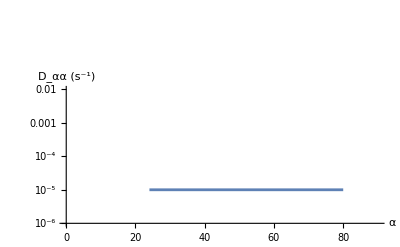

```mathematica
Dαα:=Piecewise[{{10^-3,α0<α<α1},{10^-5,α1<=α<=α2}}]
Plot[Dαα,{α,0,90},
ScalingFunctions->"Log",
PlotRange->{{0,90},{10^-6,10^-2}},
AxesLabel->{"α","D_αα (s^-1)"},
Epilog->{Text["EMIC",{20,10^-3}]}
]
```

```mathematica
"α_LC"≃α0"°"//form
"α_(0, max)"[EMIC]≃α1"°"//form
"α_(0, max)"[CH]≃α2"°"//form
```

-Graphics-

-Graphics-

-Graphics-

#### Better Form

```mathematica
jprec/jtrap=0.9/z0
```

Set::write: Tag Times in jprec/jtrap is Protected.

0.9/z0

```mathematica
SetOptions[Rasterize,RasterSize->300];
SetOptions
```

SetOptions

```mathematica
HoldForm[Subscript[D, αα][EMIC,Subscript[α, 0]<Subscript[α, 0,max][EMIC]]≃"(4 SuperscriptBox[SubscriptBox[α, LC, eq], 2])/z_0^2""1/τ_B"≃4"(α_(LC, eq))^2"(Subscript[j, prec]/Subscript[j, trap])^2"1/τ_B"]//form
HoldForm[Subscript[D, αα][EMIC,Subscript[α, 0]<Subscript[α, 0,max][EMIC]]≃4"(α_(LC, eq))^2"(Subscript[j, prec]/Subscript[j, trap])^2"1/τ_B"]//form
```

-Graphics-

-Graphics-

## Time Scale

```mathematica
Subscript[τ, EMIC]=Log[Sin[Subscript[α, o,max,EMIC]]/Sin[Subscript[α, LC]]]/(4 Subscript[D, αα,EMIC]);
Subscript[τ, CH]=Log[Sin[Subscript[α, o,max,CH]]/Sin[Subscript[α, o,max,EMIC]]]/(4 Subscript[D, αα,CH]);

(*tau_L=tau_CH+tau_EMIC*)
Subscript[τ, L]=Subscript[τ, CH]+Subscript[τ, EMIC];

(*print,tau_L*)
Subscript[τ, L]
```

Log[Csc[α_LC] Sin[ArcCos[(3.87976 √((1-c1)/((1-0.2/c1) (erg+erg^2))))/(c1 √((1/L)^4.8) L^3)]/°]]/(4 D_(αα,EMIC))+(γ^2 √(10044. (1/L)^4.+1683.55 (1/L)^3.5 Cos[1/12 (-12-69.3 (1/L)^2.+mlt) π]) Log[Csc[ArcCos[(3.87976 √((1-c1)/((1-0.2/c1) (erg+erg^2))))/(c1 √((1/L)^4.8) L^3)]/°] Sin[ArcCos[47.1206/(c2 (erg+erg^2) L^3 √(10044. (1/L)^4.+1683.55 (1/L)^3.5 Cos[1/12 (-12-69.3 (1/L)^2.+mlt) π]))]/°]] √((c2 (5.3152×10^6 per second))/L^3) (2.78422×10^16 G^2/s))/(L^6 ((5.3152×10^6 per second)/L^3)^(5/2))

## Archive

## EMIC Waves (Old)

Bounce period

```mathematica
T[y_]:=Module[{C1=1.3809,C2=-0.1851,C3=-0.4559,n=0.863},
C1+C2 y^0.5+C3 y^n
]
Subscript[T, y]:=T[y]
Subscript[τ, B]:=(4  L Subscript[R, e])/v Subscript[T, y]
```

This integral can be approximated as : j_prec/j_trap = 0.9/z_0 with less than 20 % error for z0 ∈ [0.9, 8], corresponding to jprec/jtrap ∈ [0.11, 1] .

```mathematica
SolveValues[Subscript[E, k]==(1/(√(1-v^2/c^2))-1)Subscript[m, 0] c^2/.{Subscript[m, 0]->Entity["Particle","Electron"][EntityProperty["Particle","Mass"]],c->Quantity[, "SpeedOfLight"],Subscript[E, k]->1000 Quantity[, "Kiloelectronvolts"]},{v}]
```

{{-2.821284551×10^8 m/s},{2.821284551×10^8 m/s}}

```mathematica
(*Loss cone at spacecraft*) Subscript[α, LC]=67Degree;
(*Velocity for 1 MeV electron*) v=2.82 10.*^8;
(*Local magnetic field*)magLocal=45860 Quantity[, "Nanoteslas"];
(*Corresponding equatorial magnetic field*)magEq=180 Quantity[, "Nanoteslas"];

y=(magEq/magLocal)^(1/2) Sin[Subscript[α, LC]]
Subscript[α, 0,LC,eq,ob]=ArcSin[y];
Subscript[R, e]=Entity["Planet","Earth"][EntityProperty["Planet","Radius"]];


Echo[Subscript[α, LC],"α_LC | Loss Cone at spacecraft"];
Echo[N@Subscript[α, LC,eq,ob],"α_(LC,eq,ob)| Observation-Calculated loss cone at equatorial plane"];
Echo[N@Subscript[α, LC,eq]/.{L->5.5},"α_(LC,eq)| Theoretical loss cone at equatorial plane"];
Echo[Subscript[τ, B]/.{L->5.5},"Bounce period (s)"];
```

(3 Cos[23 °])/(√2293)

α_LC | Loss Cone at spacecraft  67 °

α_(LC,eq,ob)| Observation-Calculated loss cone at equatorial plane  α_(LC,eq,ob)

α_(LC,eq)| Theoretical loss cone at equatorial plane  0.0568667

Bounce period (s)  (0.000030884 mi) T_((3 Cos[23 °])/(√2293))

```mathematica
(*SolveValues[z0==2N[Subscript[α, LC,eq]]/√(Dαα Subscript[τ, B])/.{z0->1,L->5.5},{Dαα}]*)
DααELFIN :=(4 Subscript[α, LC,eq]^2)/Subscript[z, 0]^2 1/Subscript[τ, B]
Dαα=1/8 DααELFIN 
Dαα /.{Subscript[z, 0]->8,L->5.5}
Dαα /.{Subscript[z, 0]->4,L->5.5}
Dαα /.{Subscript[z, 0]->1,L->5.5}
```

(89043. per mile)/(L √(-3 L^5+4 L^6) T_((3 Cos[23 °])/(√2293)) z_0^2)

(0.818038 per mile)/(T_((3 Cos[23 °])/(√2293)))

(3.27215 per mile)/(T_((3 Cos[23 °])/(√2293)))

(52.3544 per mile)/(T_((3 Cos[23 °])/(√2293)))